# Tuning the SOC gap and M point higher order Van Hove singularities in the surface bands of Sr_2 RuO_4

Anirudh Chandrasekaran

Loughborough University
11 June 2024

## Loading the Library

We first load the library by executing the following:

```mathematica
AppendTo[$Path,StringDelete[NotebookDirectory[],"/Sr2RuO4"]<>"Package"];
<<BandUtilities`
```

## Outline of the strategy

We will begin by loading and interpolating the tight-binding models for various values of θ and then separately load and interpolate through the models with nematic term added. We will then interpolate linearly between the nematicity free model and the model with the nematic term to generate a continuously tunable model.

## Interpolating between the Wannier90 files

### Ingredients needed for symmetrization

```mathematica
ρ={{0,-1,0},{1,0,0},{0,0,1}}; (*The matrix part of the Subscript[C, 4] rotation about one of the Ru atoms.*)
Uρ={{0,-1,0},{1,0,0},{0,0,-1}}; (*Representation of Subscript[C, 4] rotation in the d-orbital space.*)

rxy={{0,1,0},{1,0,0},{0,0,1}};  (*x<->y reflection.*)
Urxy={{-1,0,0},{0,1,0},{0,0,-1}}; (*Representation of the x<->y reflection.*)

c0={1/4,3/4,0}; (*Location of one of the Ru atoms, which we shall use as the centre of the Subscript[C, 4] rotation.*)

AtomLocations={{3/4,1/4,0},{3/4,1/4,0},{3/4,1/4,0},{1/4,3/4,0},{1/4,3/4,0},{1/4,3/4,0}}; (*Location of the basis atoms in the fractional coordinates within the unit cell.*)

SymmetryList={}; (*This is a multidimensional list which we shall construct below. Each element is a sublist corresponding to a particular symmetry. First element of the sublist is real space symmetry's matrix part, second element is the translation part and the third element is its representation in the Hilbert space. Our point group is Subscript[D, 4], or Subscript[D, 8] in some pepole's notation.*)
Do[
AppendTo[SymmetryList,{MatrixPower[ρ,i],(c0-MatrixPower[ρ,i].c0)//Simplify,ArrayFlatten[IdentityMatrix[2]⊗MatrixPower[Uρ,i]]}];

AppendTo[SymmetryList,{MatrixPower[ρ,i].rxy,(c0-MatrixPower[ρ,i].c0)//Simplify,ArrayFlatten[IdentityMatrix[2]⊗MatrixPower[Uρ,i]].ArrayFlatten[{{0,1},{1,0}}⊗Urxy]}];
,{i,1,4}];
```

### Interpolation with symmetrization

We now interpolate between the Wannier90 data for 13 different rotations of the RuO octahedra: 0° through 12° to generate a continuously θ dependent Hamiltonian, whilst ensuring that the interpolated model has the right symmetry (for which we are feeding the list SymmetryList):

```mathematica
FileLocn=NotebookDirectory[]<>"unrenormalized2/";

W90Data=LoadInterpolateTBMs[{FileLocn<>"Sr2RuO4_0deg.dat",FileLocn<>"Sr2RuO4_1deg.dat",FileLocn<>"Sr2RuO4_2deg.dat",FileLocn<>"Sr2RuO4_3deg.dat",FileLocn<>"Sr2RuO4_4deg.dat",FileLocn<>"Sr2RuO4_5deg.dat",FileLocn<>"Sr2RuO4_6deg.dat",FileLocn<>"Sr2RuO4_7deg.dat",FileLocn<>"Sr2RuO4_8deg.dat",FileLocn<>"Sr2RuO4_9deg.dat",FileLocn<>"Sr2RuO4_10deg.dat",FileLocn<>"Sr2RuO4_11deg.dat",FileLocn<>"Sr2RuO4_12deg.dat"},{0,1,2,3,4,5,6,7,8,9,10,11,12},"Symmetries"->SymmetryList,"OrbitalCentres"->AtomLocations,"ParameterSymbol"->"θ"];

Hamltn1[k1_,k2_,θ_]=W90Data[[1]];
```

Invalid or no lattice vectors provided! Using unit vectors.

Tight-binding data files loaded.

Space dimension: 3

Number of orbitals: 6

Number of supercells: 49

Number of models/data-files to interpolate: 13

Number of lines in the data files: {741,853,853,853,845,853,853,853,853,853,853,853,853}

Interpolating between the Hamiltonians.

Valid symmetrization scheme provided! We will symmetrize the loaded Hamiltonian.

Number of supercells after symmetrization: 79

## Phenomenological spin orbit term

We now construct the phenomenological SOC terms:

```mathematica
Lx={{0,0,ⅈ},{0,0,0},{-ⅈ,0,0}};
Ly={{0,0,0},{0,0,ⅈ},{0,-ⅈ,0}};
Lz={{0,-ⅈ,0},{ⅈ,0,0},{0,0,0}};

Hupup=1/2 Lz;
Hupdown=1/2(Lx+ⅈ Ly); 
Hdownup=1/2(Lx-ⅈ Ly);
Hdowndown=-1/2 Lz;
Zero2=ConstantArray[0,{3,3}];


HSOC=Join[Join[Hupup,Zero2,Hupdown,Zero2,2],Join[Zero2,Hupup,Zero2,Hupdown,2],Join[Hdownup,Zero2,Hdowndown,Zero2,2],Join[Zero2,Hdownup,Zero2,Hdowndown,2]];
```

## Reconstructing the full interpolated Hamiltonian

The full Hamiltonian incorporating SOC with tunable SOC strength and tunable θ. A version for the √2×√2 unit cell that is tailor made for fitting to the ARPES data is also defined (since the bulk has one Ru atom per unit cell, its Brillouin zone has twice the area of the default surface band BZ, which is also ‘rotated’ by 45°).

```mathematica
Hamiltonian1[k1_,k2_,θ_,λ_]=0.5(ArrayFlatten[IdentityMatrix[2]⊗Hamltn1[k1,k2,θ]]+λ HSOC+ComplexExpand[ConjugateTranspose[ArrayFlatten[IdentityMatrix[2]⊗Hamltn1[k1,k2,θ]]+λ HSOC]]);
```

We can check the eigenvalues at a high symmetry point to see if the symmetrisation was successful, and has eliminated the weak splitting of degeneracies at the high symmetry points

## Loading and interpolating the nematic models

```mathematica
FileLocn2=NotebookDirectory[]<>"renormalized/";

W90Data2=LoadInterpolateTBMs[{FileLocn2<>"Sr2RuO4_EXP_Monolayer_1theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_1theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_2theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_3theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_4theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_5theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_6theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_7theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_8theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_9theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_10theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_11theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_12theta_0phi1_0phi2_hr_sym_soc_nem.dat"},{0,1,2,3,4,5,6,7,8,9,10,11,12},"ParameterSymbol"->"θ"];

Hamiltonian2[k1_,k2_,θ_]=W90Data2[[1]];
```

Invalid or no lattice vectors provided! Using unit vectors.

Tight-binding data files loaded.

Space dimension: 3

Number of orbitals: 12

Number of supercells: 49

Number of models/data-files to interpolate: 13

Number of lines in the data files: {1723,1723,1723,1723,1707,1723,1723,1723,1723,1723,1723,1723,1723}

Interpolating between the Hamiltonians.

No valid symmetrization scheme provided! We will not symmetrize the loaded Hamiltonian.

## Comparing the nematic and symmetric models

For the sake of plotting, let us define the Hamiltonians evaluated at θ=8° with and without the nematic term

```mathematica
HamTemp[k_]:=1000 0.2444Hamiltonian1[k[[1]]-k[[2]],k[[1]]+k[[2]],8,0.175]
HamTempNem[k_]:=1000Hamiltonian2[k[[1]]-k[[2]],k[[1]]+k[[2]],8]
```

Using these the bands can be generated

```mathematica
HSymmPts={{{0,π-3.869  0.36},"← Γ"},{{0,π},"M_y"},{{3.869 0.36,π},"X →"}};
Bnd1=GenerateBandStructure[HamTemp,HSymmPts];
Bnd2=GenerateBandStructure[HamTempNem,HSymmPts];
```

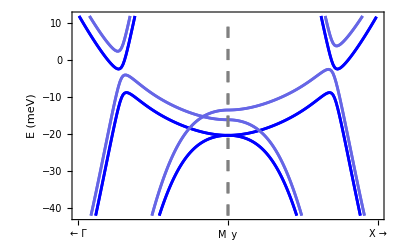

```mathematica
plt1=PlotBandStructure[Bnd1,{-42,12},"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[0,0,1]}];

plt2=PlotBandStructure[Bnd2,{-42,12},"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[0.4,0.4,0.9]}];

Show[plt1,plt2]
```

The degeneracy at the M_y point has been lifted which is to be expected since the nematic term breaks the r_xy reflection symmetry that causes the degeneracy.

## A continuously θ(°) and Δ_nem(%) tuned model

```mathematica
HamiltonianNemTunedmeV[k1_,k2_,θ_,Δ_]=(1-Δ)1000 0.2444Hamiltonian1[k1-k2,k1+k2,θ,0.175]+1000Δ Hamiltonian2[k1-k2,k1+k2,θ];

HamltnTuned[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],k[[4]]]

HamTempNem2[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],8,2(*Nematicity set to 2%*)]
```

#### Checking the interpolation

```mathematica
Bnd3=GenerateBandStructure[HamTempNem2,HSymmPts];
```

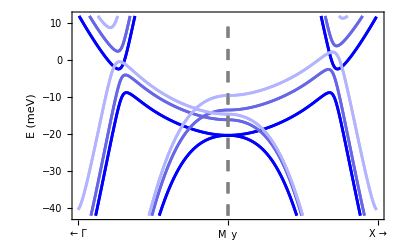

```mathematica
plt3=PlotBandStructure[Bnd3,{-42,12},"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[0.7,0.7,1]}];

Show[plt1,plt2,plt3]
```

We can see that the interpolation scheme has worked.

### Iterating through Δ_nem and hunting for HOS

Let us outline the strategy that we shall adopt below. We iterate through a few values of Δ_nem including 0%, 1% and 2%. At each Δ_nem, we will try to tune the M point singularity and the SOC gap critical points to a HOS. We note down the θ_crit and the series expansion of the four bands.

Now the bands(points) of interest are 5&6(M point), 7&8(M point), 7&8(SOC gap) and 9&10(SOC gap). For 5&6(M point) and 7&8(M point), tuning to HOS is simpler. We are already at a critical point, namely the high symmetry M point. We compute det(Hes) as a function of δθ and set it to zero to solve for δθ. If we repeat this a few times we get θ_crit. But for the SOC gap critical points, we have to adopt a different strategy since the location of the critical point is not fixed and changes with θ and Δ_nem.

We will use a two-pronged strategy: first we choose a range of θ to investigate, say 8° to 10°. We locate the k_VHS for the angles at the end points of the range and compute the Hessian determinant. If they are of opposite sign, we expect the Hessian determinant to vanish somewhere in between. We will then use binary search to locate this θ_crit. We have to do this separately for both the bands, and on either sides of the SOC gap (which have been made inequivalent by the nematic term).

Firstly, we have to identify the range of k in which the SOC critical points seem to exist by plotting the dispersion for Δ_nem= 0%, 1%, 2% and 4% and θ=7°,8°,...,11°. This is needed since we need to identify a suitable range for the LocateCriticalPoint routine to work to find the actual k_VHS.

## Evolution of the band-structure

We plot a spaghetti plot showing the evolution of the band-structure with θ for different choices of Δ_nem (0%, 1% and 2%).

```mathematica
HSymmPtsNoLabel={{{0,π-3.869  0.35},""},{{0,π},""},{{3.869 0.35,π},""}};
AngleList={7,8,9,10,11};

OpacityList={0.1,0.2,0.35,0.5,1};
ColourChoice={67/255,49/255,12/255}(*{45/255,38/255,87/255}*); (*This for one choice of colour scheme - with a fixed colour and varying transparency given by the alpha channel.*)
```

### 1) Δ_nem=0%

```mathematica
BandDataList1=First@Last@Reap[Do[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],angle,0.];

Sow[GenerateBandStructure[HamCurr,HSymmPts]];
,{angle,AngleList}]];
```

```mathematica
BandPlotList1=First@Last@Reap[Do[
Sow[PlotBandStructure[BandDataList1[[i]],{-42,12}(*meV range*),"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[ColourChoice[[1]],ColourChoice[[2]],ColourChoice[[3]],OpacityList[[i]]]},"PlotKeyLegend"->{Style[ToString[AngleList[[i]]],FontSize->8,FontFamily->"Times"],Scaled[{0.31,1.01-i/19.}]}]];
,{i,1,Length[AngleList]}]];
```

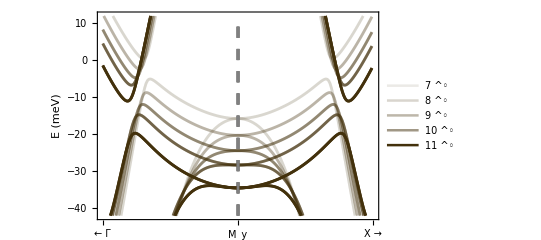

```mathematica
SpaghettiPlot1=Show[BandPlotList1]
```

### 2) Δ_nem=1%

```mathematica
BandDataList2=First@Last@Reap[Do[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],angle,1.];

Sow[GenerateBandStructure[HamCurr,HSymmPts]];
,{angle,AngleList}]];
```

```mathematica
BandPlotList2=First@Last@Reap[Do[
Sow[PlotBandStructure[BandDataList2[[i]],{-42,12}(*meV range*),"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[ColourChoice[[1]],ColourChoice[[2]],ColourChoice[[3]],OpacityList[[i]]]},"PlotKeyLegend"->{Style[ToString[AngleList[[i]]],FontSize->8,FontFamily->"Times"],Scaled[{0.31,1.01-i/19.}]}]];
,{i,1,Length[AngleList]}]];
```

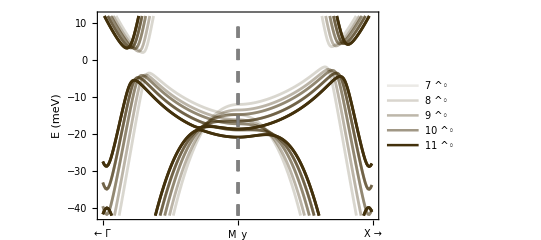

```mathematica
SpaghettiPlot2=Show[BandPlotList2]
```

### 3) Δ_nem=2%

```mathematica
BandDataList3=First@Last@Reap[Do[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],angle,2.];

Sow[GenerateBandStructure[HamCurr,HSymmPts]];
,{angle,AngleList}]];
```

```mathematica
BandPlotList3=First@Last@Reap[Do[
Sow[PlotBandStructure[BandDataList3[[i]],{-25,25}(*meV range*),"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[ColourChoice[[1]],ColourChoice[[2]],ColourChoice[[3]],OpacityList[[i]]]},"PlotKeyLegend"->{Style[ToString[AngleList[[i]]],FontSize->8,FontFamily->"Times"],Scaled[{0.31,1.01-i/19.}]}]];
,{i,1,Length[AngleList]}]];
```

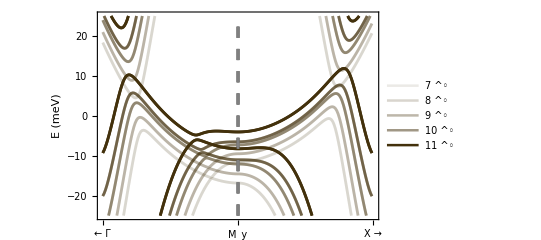

```mathematica
SpaghettiPlot3=Show[BandPlotList3]
```

### 3) Δ_nem=4%

```mathematica
BandDataList4=First@Last@Reap[Do[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],angle,4.];

Sow[GenerateBandStructure[HamCurr,HSymmPts]];
,{angle,AngleList}]];
```

```mathematica
BandPlotList4=First@Last@Reap[Do[
Sow[PlotBandStructure[BandDataList4[[i]],{-40,80}(*meV range*),"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[ColourChoice[[1]],ColourChoice[[2]],ColourChoice[[3]],OpacityList[[i]]]},"PlotKeyLegend"->{Style[ToString[AngleList[[i]]],FontSize->8,FontFamily->"Times"],Scaled[{0.31,1.01-i/19.}]}]];
,{i,1,Length[AngleList]}]];
```

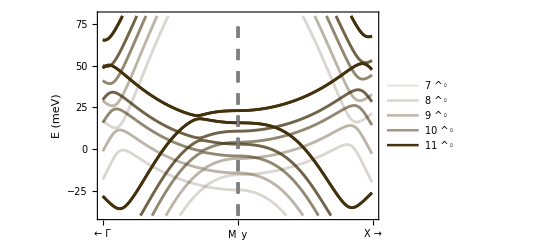

```mathematica
SpaghettiPlot4=Show[BandPlotList4]
```

## Evolution of the nature of the critical points in the SOC gap

In this section, we look at the evolution of the nature of the critical points as we change Δ_nem and θ, that is whether they are maxima, minima or saddles.

### Upper VHS - Band 9, part 1

```mathematica
Do[
Print["Δ_nem=",Delt,"%:"];

Do[

HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θCurr,Delt];

kVHSTrialLow={0.6 3.869 0.36,π//N};
kVHSTrialUp={3.869 0.36,π//N};

(*Finding true kVHS:*)
{kVHS,CritPtFound}=LocateCriticalPoint[HamCurr,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

If[CritPtFound==True,
TaylorPoly=Chop[Total[TaylorExpandBand[HamCurr,kVHS,9,2,"Messages"->False][[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]},10^-2];

Print["\t","θ = ",θCurr,", k_crit = ",kVHS,", Tayl = ",TaylorPoly];
,
Print["Critical point could not be found for θ = ",θCurr];
]

,{θCurr,8,11,1}];

,{Delt,0,4,1(*0.25*)}];
```

Δ_nem=0%:

θ = 8, k_crit = {1.01581,3.14159}, Tayl = -2.36331+529.026 k_x^2-9.47938 k_y^2

θ = 9, k_crit = {1.05733,3.14159}, Tayl = -4.71827+503.4 k_x^2+4.02982 k_y^2

θ = 10, k_crit = {1.09814,3.14159}, Tayl = -6.73067+483.824 k_x^2+16.2413 k_y^2

θ = 11, k_crit = {1.13796,3.14159}, Tayl = -11.0382+472.719 k_x^2+26.8556 k_y^2

Δ_nem=1%:

θ = 8, k_crit = {1.00831,3.14159}, Tayl = 3.88659+508.026 k_x^2-10.0838 k_y^2

θ = 9, k_crit = {1.05033,3.14159}, Tayl = 4.459+485.567 k_x^2+3.53534 k_y^2

θ = 10, k_crit = {1.09162,3.14159}, Tayl = 4.5194+467.958 k_x^2+15.8555 k_y^2

θ = 11, k_crit = {1.13192,3.14159}, Tayl = 4.30303+458.082 k_x^2+26.5837 k_y^2

Δ_nem=2%:

θ = 8, k_crit = {1.06639,3.14159}, Tayl = 11.3763+416.234 k_x^2-13.2742 k_y^2

θ = 9, k_crit = {1.10587,3.14159}, Tayl = 15.7941+403.497 k_x^2-0.812546 k_y^2

θ = 10, k_crit = {1.1442,3.14159}, Tayl = 18.8672+398.826 k_x^2+10.2062 k_y^2

θ = 11, k_crit = {1.18092,3.14159}, Tayl = 23.7056+404.734 k_x^2+19.483 k_y^2

Δ_nem=3%:

θ = 8, k_crit = {1.15559,3.14159}, Tayl = 19.6969+388.477 k_x^2-17.618 k_y^2

θ = 9, k_crit = {1.19051,3.14159}, Tayl = 28.3895+383.784 k_x^2-7.04354 k_y^2

θ = 10, k_crit = {1.22406,3.14159}, Tayl = 34.8767+388.926 k_x^2+2.14796 k_y^2

θ = 11, k_crit = {1.25604,3.14159}, Tayl = 45.1184+405.141 k_x^2+9.79735 k_y^2

Δ_nem=4%:

θ = 8, k_crit = {1.25345,3.14159}, Tayl = 29.0708+404.815 k_x^2-21.4064 k_y^2

θ = 9, k_crit = {1.28423,3.14159}, Tayl = 42.0426+404.599 k_x^2-12.7704 k_y^2

θ = 10, k_crit = {1.31408,3.14159}, Tayl = 51.9031+413.994 k_x^2-5.23332 k_y^2

θ = 11, k_crit = {1.34329,3.14159}, Tayl = 67.4569+432.759 k_x^2+1.15399 k_y^2

We see that all the HOS points indeed likely lie in the range [8°,11°] since the coefficient of k_y^2 changes sign for all the values of Δ_nem in this range. Also, the critical point changes from an ordinary saddle to an ordinary minimum as we increase θ at each Δ_nem. Now for band 8 (downward dispersing):

### Lower VHS - Band 8, part 1

```mathematica
Do[
Print["Δ_nem=",Delt,"%:"];

Do[

HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θCurr,Delt];

kVHSTrialLow={0.5 3.869 0.35,π//N};
kVHSTrialUp={0.9 3.869 0.35,π//N};

(*Finding true kVHS:*)
{kVHS,CritPtFound}=LocateCriticalPoint[HamCurr,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->False,"MaxIterations"->28,"Resolution"->10^-2];

If[CritPtFound==True,
TaylorPoly=Chop[Total[TaylorExpandBand[HamCurr,kVHS,8,2,"Messages"->False][[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]},10^-2];

Print["\t","θ = ",θCurr,", k_crit = ",kVHS,", Tayl = ",TaylorPoly];
,
Print["Critical point could not be found for θ = ",θCurr];
]

,{θCurr,8,11,1}];

,{Delt,0,3,1(*0.25*)}];
```

Δ_nem=0%:

θ = 8, k_crit = {0.943277,3.14159}, Tayl = -8.71343-417.359 k_x^2-12.3465 k_y^2

θ = 9, k_crit = {0.981329,3.14159}, Tayl = -11.9083-400.277 k_x^2+1.12069 k_y^2

θ = 10, k_crit = {1.02021,3.14159}, Tayl = -14.7072-388.262 k_x^2+13.1978 k_y^2

θ = 11, k_crit = {1.06041,3.14159}, Tayl = -19.695-382.709 k_x^2+23.3541 k_y^2

Δ_nem=1%:

θ = 8, k_crit = {0.933392,3.14159}, Tayl = -2.42802-395.894 k_x^2-12.9932 k_y^2

θ = 9, k_crit = {0.971956,3.14159}, Tayl = -2.69943-381.479 k_x^2+0.585187 k_y^2

θ = 10, k_crit = {1.01135,3.14159}, Tayl = -3.43275-371.822 k_x^2+12.7885 k_y^2

θ = 11, k_crit = {1.05201,3.14159}, Tayl = -4.34178-367.689 k_x^2+23.0969 k_y^2

Δ_nem=2%:

θ = 8, k_crit = {0.970287,3.14159}, Tayl = 2.26882-310.083 k_x^2-16.7735 k_y^2

θ = 9, k_crit = {1.00791,3.14159}, Tayl = 5.59709-304.037 k_x^2-4.49169 k_y^2

θ = 10, k_crit = {1.04781,3.14159}, Tayl = 7.72889-304.834 k_x^2+6.01401 k_y^2

θ = 11, k_crit = {1.09056,3.14159}, Tayl = 11.8771-313.623 k_x^2+13.9943 k_y^2

Δ_nem=3%:

θ = 8, k_crit = {1.05042,3.14159}, Tayl = 7.27525-293.395 k_x^2-20.7362 k_y^2

θ = 9, k_crit = {1.08798,3.14159}, Tayl = 14.7984-292.943 k_x^2-10.7027 k_y^2

θ = 10, k_crit = {1.12924,3.14159}, Tayl = 20.4623-301.146 k_x^2-2.82157 k_y^2

θ = 11, k_crit = {1.17407,3.14159}, Tayl = 30.366-318.71 k_x^2+2.28758 k_y^2

Here too we see that for all the Δ_nem the HOS likely lies in the range [8°,11°]. Also, we see that the critical point changes from an ordinary maximum to an ordinary saddle as we increase θ at each Δ_nem up to 3%.

## Using binary search to find HOVHs in the SOC gap

### Band 9, part 1

```mathematica
NoIterns=5;
CurrResln=10^-2;
kVHSTrialLow={0.6 3.869 0.36,π//N};
kVHSTrialUp={3.869 0.36,π//N};

HosListBand9={};
SetSharedVariable[HosListBand9];

ParallelDo[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],Delt];

NoTry=0;
HOSFound=False;
HOSPossible=True;
θmax=10;
θmin=8;

(*Print["Binary search initiated for Δ_nem = ",Delt];*)

While[NoTry<=14&&HOSFound==False&&HOSPossible==True,
HamCurrUp[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmax,Delt];
HamCurrDown[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmin,Delt];

(*We compute the Hessian determinant for Subscript[θ, max]*)
(*Finding true kVHS:*)
{kVHSmax,CritPtFound}=LocateCriticalPoint[HamCurrUp,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

TaylorPolyMax=TaylorExpandBand[HamCurrUp,kVHSmax,9,2,"Messages"->False];

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMax=Chop[TaylorPolyMax,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMax=(D[TaylorPolyMax[[1,3]],{p1,2}]D[TaylorPolyMax[[1,3]],{p2,2}]-(D[TaylorPolyMax[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

(*We now compute the Hessian determinant for Subscript[θ, min]*)
(*Finding true kVHS:*)
{kVHSmin,CritPtFound}=LocateCriticalPoint[HamCurrDown,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

TaylorPolyMin=TaylorExpandBand[HamCurrDown,kVHSmin,9,2,"Messages"->False];

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMin=Chop[TaylorPolyMin,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMin=(D[TaylorPolyMin[[1,3]],{p1,2}]D[TaylorPolyMin[[1,3]],{p2,2}]-(D[TaylorPolyMin[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

(*Now we begin the binary search if the Hessian determinants computed above are opposite in sign*)
If[Sign[HesDetMax]==-Sign[HesDetMin]&&HOSFound==False&&HOSPossible==True,

θmid=0.5(θmax+θmin);
HamCurrMid[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmid,Delt];

(*Finding true kVHS1:*)
{kVHSmid,CritPtFound}=LocateCriticalPoint[HamCurrMid,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

TaylorPolyMid=TaylorExpandBand[HamCurrMid,kVHSmid,9,2,"Messages"->False];

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMid=Chop[TaylorPolyMid,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMid=(D[TaylorPolyMid[[1,3]],{p1,2}]D[TaylorPolyMid[[1,3]],{p2,2}]-(D[TaylorPolyMid[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMid=Chop[TaylorPolyMid,CurrResln];

HesDet=(D[TaylorPolyMid[[1,3]],{p1,2}]D[TaylorPolyMid[[1,3]],{p2,2}]-(D[TaylorPolyMid[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[Chop[HesDet,1.]==0,
HOSFound=True;
,
If[Sign[HesDet]==Sign[HesDetMax],
θmax=θmid;
,
If[Sign[HesDet]==Sign[HesDetMin],
θmin=θmid;
]
]
];

NoTry++;
,
If[HOSFound==False,
Print[Style["No HOS in the range!",Red]];
HOSPossible=False;
]
];
];

If[HOSFound==True,
Print["Δ_nem = ",Delt,". Binary search converged after ",NoTry," iterations."];
Print["θ_crit=",θmid,", det[Hes]=",HesDet,", Tayl = ",Chop[Total[TaylorPolyMid[[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]}]];
AppendTo[HosListBand9,{Delt,θmid}];
,
Print[Style["No HOS in the range!",Red]];
];
,{Delt,0,3,0.25}]
```

Δ_nem = 1.. Binary search converged after 7 iterations.

θ_crit=8.73438, det[Hes]=0., Tayl = 4.23394+491.382 k_x^2

Δ_nem = 3.. Binary search converged after 8 iterations.

θ_crit=9.74219, det[Hes]=0., Tayl = 33.8245+386.602 k_x^2

Δ_nem = 0.. Binary search converged after 8 iterations.

θ_crit=8.69531, det[Hes]=0., Tayl = -4.0873+511.035 k_x^2

Δ_nem = 0.5. Binary search converged after 8 iterations.

θ_crit=8.67969, det[Hes]=0., Tayl = -0.224357+524.967 k_x^2

Δ_nem = 2.5. Binary search converged after 10 iterations.

θ_crit=9.35742, det[Hes]=0., Tayl = 24.2157+385.642 k_x^2

Δ_nem = 2.. Binary search converged after 10 iterations.

θ_crit=9.06836, det[Hes]=0., Tayl = 16.1091+402.723 k_x^2

Δ_nem = 2.75. Binary search converged after 10 iterations.

θ_crit=9.53711, det[Hes]=0., Tayl = 28.8717+384.118 k_x^2

Δ_nem = 1.5. Binary search converged after 11 iterations.

θ_crit=8.8623, det[Hes]=0., Tayl = 9.56419+440.202 k_x^2

Δ_nem = 1.25. Binary search converged after 8 iterations.

θ_crit=8.78906, det[Hes]=0., Tayl = 6.77168+465.273 k_x^2

Δ_nem = 0.25. Binary search converged after 11 iterations.

θ_crit=8.67871, det[Hes]=0., Tayl = -2.2114+523.537 k_x^2

Δ_nem = 2.25. Binary search converged after 10 iterations.

θ_crit=9.20117, det[Hes]=0., Tayl = 19.9499+391.846 k_x^2

Δ_nem = 0.75. Binary search converged after 11 iterations.

θ_crit=8.69824, det[Hes]=0., Tayl = 1.91293+513.132 k_x^2

Δ_nem = 1.75. Binary search converged after 10 iterations.

θ_crit=8.95508, det[Hes]=0., Tayl = 12.6591+418.975 k_x^2

```mathematica
HosListBand9=SortBy[HosListBand9,First]
```

{{0.,8.69531},{0.25,8.67871},{0.5,8.67969},{0.75,8.69824},{1.,8.73438},{1.25,8.78906},{1.5,8.8623},{1.75,8.95508},{2.,9.06836},{2.25,9.20117},{2.5,9.35742},{2.75,9.53711},{3.,9.74219}}

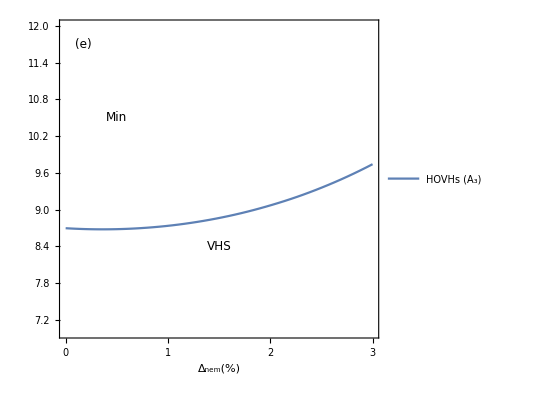

```mathematica
FitFunc1=Interpolation[HosListBand9];
PlotBand9=ListPlot[HosListBand9];
PanelE=Show[(*PlotBand9,*)Plot[FitFunc1[x],{x,0,3},FrameLabel->{"Δ_nem(%)",(*"θ(°)"*)None},PlotLegends->Placed[{Style["HOVHs (A_3)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{0,3},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{0,1,2,3},None}}],Graphics[Text[Style["VHS",FontFamily->"Arial",FontSize->12],{1.5,8.4}]],Graphics[Text[Style["Min",FontFamily->"Arial",FontSize->12],{0.5,10.5}]],Graphics[Text[Style["(e)",FontFamily->"Arial",FontSize->12],{0.175,11.7}]]]
```

### Band 8, part 1

```mathematica
NoIterns=5;
CurrResln=10^-2;
kVHSTrialLow={0.5 3.869 0.35,π//N};
kVHSTrialUp={0.9 3.869 0.35,π//N};

HosListBand8={};
SetSharedVariable[HosListBand8];

ParallelDo[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],Delt];

NoTry=0;
HOSFound=False;
HOSPossible=True;
θmax=11;
θmin=8;

(*Print["Binary search initiated for Δ_nem = ",Delt];*)

While[NoTry<=18&&HOSFound==False&&HOSPossible==True,
HamCurrUp[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmax,Delt];
HamCurrDown[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmin,Delt];

(*We compute the Hessian determinant for Subscript[θ, max]*)
(*Finding true kVHS:*)
{kVHSmax,CritPtFound}=LocateCriticalPoint[HamCurrUp,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->True,"MaxIterations"->28,"Resolution"->10^-2];

TaylorPolyMax=TaylorExpandBand[HamCurrUp,kVHSmax,8,2,"Messages"->False];
TaylorPolyMax=Chop[TaylorPolyMax,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMax=(D[TaylorPolyMax[[1,3]],{p1,2}]D[TaylorPolyMax[[1,3]],{p2,2}]-(D[TaylorPolyMax[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
(*Print["Critical point not found for θ_max at Δ_nem = ",Delt,"."];*)
];


(*We now compute the Hessian determinant for Subscript[θ, min]*)
(*Finding true kVHS:*)
{kVHSmin,CritPtFound}=LocateCriticalPoint[HamCurrDown,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->True,"MaxIterations"->28,"Resolution"->10^-2];

TaylorPolyMin=TaylorExpandBand[HamCurrDown,kVHSmin,8,2,"Messages"->False];
TaylorPolyMin=Chop[TaylorPolyMin,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMin=(D[TaylorPolyMin[[1,3]],{p1,2}]D[TaylorPolyMin[[1,3]],{p2,2}]-(D[TaylorPolyMin[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
(*Print["Critical point not found for θ_min at Δ_nem = ",Delt,"."];*)
];

(*Now we begin the binary search if the Hessian determinants computed above are opposite in sign*)
If[Sign[HesDetMax]==-Sign[HesDetMin]&&HOSFound==False&&HOSPossible==True,

θmid=0.5(θmax+θmin);
HamCurrMid[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmid,Delt];

(*Finding true kVHS1:*)
{kVHSmid,CritPtFound}=LocateCriticalPoint[HamCurrMid,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->True,"MaxIterations"->28,"Resolution"->10^-2];

TaylorPolyMid=TaylorExpandBand[HamCurrMid,kVHSmid,8,2,"Messages"->False];
TaylorPolyMid=Chop[TaylorPolyMid,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMid=(D[TaylorPolyMid[[1,3]],{p1,2}]D[TaylorPolyMid[[1,3]],{p2,2}]-(D[TaylorPolyMid[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
(*Print["Critical point not found for θ_mid at Δ_nem = ",Delt,"."];*)
];


If[Chop[HesDetMid,1.]==0,
HOSFound=True;
,
If[Sign[HesDetMid]==Sign[HesDetMax],
θmax=θmid;
,
If[Sign[HesDetMid]==Sign[HesDetMin],
θmin=θmid;
]
]
];

NoTry++;
,
If[HOSFound==False,
Print[Style["No HOS in the range!",Red]];
HOSPossible=False;
]
];
];

If[HOSFound==True,
Print["Δ_nem = ",Delt,". Binary search converged after ",NoTry," iterations."];
Print["θ_crit=",θmid,", det[Hes]=",HesDetMid,", Tayl = ",Chop[Total[TaylorPolyMid[[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]}]];
AppendTo[HosListBand8,{Delt,θmid}];
,
Print[Style["No HOS in the range!",Red]];
];
,{Delt,0,3,0.25}]
```

Δ_nem = 0.. Binary search converged after 7 iterations.

θ_crit=8.91406, det[Hes]=0., Tayl = -11.6625-401.535 k_x^2

Δ_nem = 3.. Binary search converged after 8 iterations.

θ_crit=10.5664, det[Hes]=-0.000106631, Tayl = 22.8522-310.467 k_x^2-0.0103262 k_x k_y

Δ_nem = 2.. Binary search converged after 8 iterations.

θ_crit=9.39453, det[Hes]=0., Tayl = 6.87135-302.988 k_x^2

Δ_nem = 1.. Binary search converged after 9 iterations.

θ_crit=8.95508, det[Hes]=0., Tayl = -2.69961-382.237 k_x^2

Δ_nem = 0.5. Binary search converged after 9 iterations.

θ_crit=8.88477, det[Hes]=0., Tayl = -6.94277-414.511 k_x^2

Δ_nem = 2.75. Binary search converged after 10 iterations.

θ_crit=10.1064, det[Hes]=0., Tayl = 17.2836-298.616 k_x^2

Δ_nem = 2.5. Binary search converged after 10 iterations.

θ_crit=9.80176, det[Hes]=0., Tayl = 13.4432-294.303 k_x^2

Δ_nem = 1.5. Binary search converged after 11 iterations.

θ_crit=9.12646, det[Hes]=0., Tayl = 1.66114-334.565 k_x^2

Δ_nem = 2.25. Binary search converged after 9 iterations.

θ_crit=9.57617, det[Hes]=0., Tayl = 9.97966-295.728 k_x^2

Δ_nem = 0.25. Binary search converged after 11 iterations.

θ_crit=8.88623, det[Hes]=0., Tayl = -9.21966-413.253 k_x^2

Δ_nem = 1.25. Binary search converged after 10 iterations.

θ_crit=9.02832, det[Hes]=0., Tayl = -0.581924-357.603 k_x^2

Δ_nem = 0.75. Binary search converged after 11 iterations.

θ_crit=8.90674, det[Hes]=0., Tayl = -4.78992-402.981 k_x^2

Δ_nem = 1.75. Binary search converged after 9 iterations.

θ_crit=9.24805, det[Hes]=0., Tayl = 4.12031-315.973 k_x^2

```mathematica
HosListBand8=SortBy[HosListBand8,First]
```

{{0.,8.91406},{0.25,8.88623},{0.5,8.88477},{0.75,8.90674},{1.,8.95508},{1.25,9.02832},{1.5,9.12646},{1.75,9.24805},{2.,9.39453},{2.25,9.57617},{2.5,9.80176},{2.75,10.1064},{3.,10.5664}}

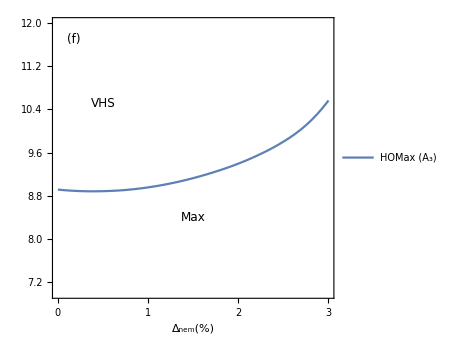

```mathematica
FitFunc2=Interpolation[HosListBand8];
PlotBand8=ListPlot[HosListBand8];
PanelF=Show[(*PlotBand9,*)Plot[FitFunc2[x],{x,0,3},FrameLabel->{"Δ_nem(%)",(*"θ(°)"*)None},PlotLegends->Placed[{Style["HOMax (A_3)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{0,3},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{0,1,2,3},None}}],Graphics[Text[Style["Max",FontFamily->"Arial",FontSize->12],{1.5,8.4}]],Graphics[Text[Style["VHS",FontFamily->"Arial",FontSize->12],{0.5,10.5}]],Graphics[Text[Style["(f)",FontFamily->"Arial",FontSize->12],{0.175,11.7}]]]
```

### Band 9, part 2

```mathematica
NoIterns=5;
CurrResln=10^-2;
kVHSTrialLow={0,π-3.869 0.36};
kVHSTrialUp={0,π-0.6 3.869 0.36};

HosListBand9p2={};
SetSharedVariable[HosListBand9p2];

ParallelDo[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],Delt];

NoTry=0;
HOSFound=False;
HOSPossible=True;
θmax=10;
θmin=8;

(*Print["Binary search initiated for Δ_nem = ",Delt];*)

While[NoTry<=14&&HOSFound==False&&HOSPossible==True,
HamCurrUp[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmax,Delt];
HamCurrDown[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmin,Delt];

(*We compute the Hessian determinant for Subscript[θ, max]*)
(*Finding true kVHS:*)
{kVHSmax,CritPtFound}=LocateCriticalPoint[HamCurrUp,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

TaylorPolyMax=TaylorExpandBand[HamCurrUp,kVHSmax,9,2,"Messages"->False];

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMax=Chop[TaylorPolyMax,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMax=(D[TaylorPolyMax[[1,3]],{p1,2}]D[TaylorPolyMax[[1,3]],{p2,2}]-(D[TaylorPolyMax[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

(*We now compute the Hessian determinant for Subscript[θ, min]*)
(*Finding true kVHS:*)
{kVHSmin,CritPtFound}=LocateCriticalPoint[HamCurrDown,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

TaylorPolyMin=TaylorExpandBand[HamCurrDown,kVHSmin,9,2,"Messages"->False];

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMin=Chop[TaylorPolyMin,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMin=(D[TaylorPolyMin[[1,3]],{p1,2}]D[TaylorPolyMin[[1,3]],{p2,2}]-(D[TaylorPolyMin[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

(*Now we begin the binary search if the Hessian determinants computed above are opposite in sign*)
If[Sign[HesDetMax]==-Sign[HesDetMin]&&HOSFound==False&&HOSPossible==True,

θmid=0.5(θmax+θmin);
HamCurrMid[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmid,Delt];

(*Finding true kVHS1:*)
{kVHSmid,CritPtFound}=LocateCriticalPoint[HamCurrMid,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

TaylorPolyMid=TaylorExpandBand[HamCurrMid,kVHSmid,9,2,"Messages"->False];

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMid=Chop[TaylorPolyMid,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMid=(D[TaylorPolyMid[[1,3]],{p1,2}]D[TaylorPolyMid[[1,3]],{p2,2}]-(D[TaylorPolyMid[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMid=Chop[TaylorPolyMid,CurrResln];

HesDet=(D[TaylorPolyMid[[1,3]],{p1,2}]D[TaylorPolyMid[[1,3]],{p2,2}]-(D[TaylorPolyMid[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[Chop[HesDet,1.]==0,
HOSFound=True;
,
If[Sign[HesDet]==Sign[HesDetMax],
θmax=θmid;
,
If[Sign[HesDet]==Sign[HesDetMin],
θmin=θmid;
]
]
];

NoTry++;
,
If[HOSFound==False,
Print[Style["No HOS in the range!",Red]];
HOSPossible=False;
]
];
];

If[HOSFound==True,
Print["Δ_nem = ",Delt,". Binary search converged after ",NoTry," iterations."];
Print["θ_crit=",θmid,", det[Hes]=",HesDet,", Tayl = ",Chop[Total[TaylorPolyMid[[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]}]];
AppendTo[HosListBand9p2,{Delt,θmid}];
,
Print[Style["No HOS in the range!",Red]];
];
,{Delt,0,3,0.25}]
```

Δ_nem = 1.. Binary search converged after 6 iterations.

θ_crit=8.65625, det[Hes]=0., Tayl = 2.82964+531.172 k_y^2

Δ_nem = 0.5. Binary search converged after 7 iterations.

θ_crit=8.64063, det[Hes]=0., Tayl = -0.87683+546.402 k_y^2

Δ_nem = 2.5. Binary search converged after 8 iterations.

θ_crit=9.17969, det[Hes]=0., Tayl = 20.6695+448.428 k_y^2

Δ_nem = 0.. Binary search converged after 8 iterations.

θ_crit=8.69531, det[Hes]=0., Tayl = -4.0873+511.035 k_y^2

Δ_nem = 3.. Binary search converged after 8 iterations.

θ_crit=9.53906, det[Hes]=0., Tayl = 30.1774+455.236 k_y^2

Δ_nem = 2.75. Binary search converged after 9 iterations.

θ_crit=9.34766, det[Hes]=0., Tayl = 25.2007+449.627 k_y^2

Δ_nem = 2.. Binary search converged after 10 iterations.

θ_crit=8.91992, det[Hes]=0., Tayl = 13.1493+460.175 k_y^2

Δ_nem = 1.5. Binary search converged after 11 iterations.

θ_crit=8.74707, det[Hes]=0., Tayl = 7.36585+491.107 k_y^2

Δ_nem = 1.25. Binary search converged after 9 iterations.

θ_crit=8.69141, det[Hes]=0., Tayl = 4.97067+511.489 k_y^2

Δ_nem = 0.75. Binary search converged after 10 iterations.

θ_crit=8.63867, det[Hes]=0., Tayl = 0.893552+544.51 k_y^2

Δ_nem = 2.25. Binary search converged after 8 iterations.

θ_crit=9.03906, det[Hes]=0., Tayl = 16.6685+451.938 k_y^2

Δ_nem = 0.25. Binary search converged after 10 iterations.

θ_crit=8.6582, det[Hes]=0., Tayl = -2.52023+534.12 k_y^2

Δ_nem = 1.75. Binary search converged after 10 iterations.

θ_crit=8.82227, det[Hes]=0., Tayl = 10.0679+473.456 k_y^2

```mathematica
HosListBand9p2=SortBy[HosListBand9p2,First]
```

{{0.,8.69531},{0.25,8.6582},{0.5,8.64063},{0.75,8.63867},{1.,8.65625},{1.25,8.69141},{1.5,8.74707},{1.75,8.82227},{2.,8.91992},{2.25,9.03906},{2.5,9.17969},{2.75,9.34766},{3.,9.53906}}

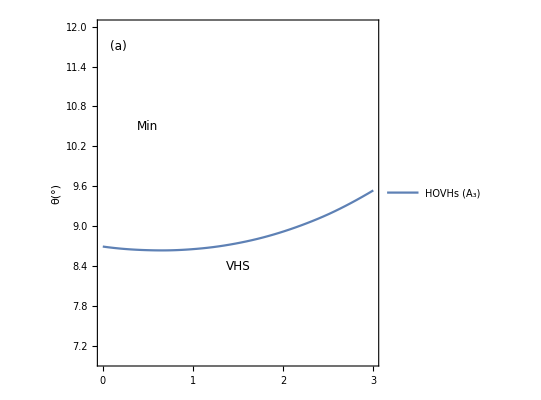

```mathematica
FitFunc3=Interpolation[HosListBand9p2];
PlotBand9p2=ListPlot[HosListBand9p2];
PanelA=Show[(*PlotBand9,*)Plot[FitFunc3[x],{x,0,3},FrameLabel->{(*"Δ_nem(%)"*)None,"θ(°)"},PlotLegends->Placed[{Style["HOVHs (A_3)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{0,3},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{0,1,2,3},None}}],Graphics[Text[Style["VHS",FontFamily->"Arial",FontSize->12],{1.5,8.4}]],Graphics[Text[Style["Min",FontFamily->"Arial",FontSize->12],{0.5,10.5}]],Graphics[Text[Style["(a)",FontFamily->"Arial",FontSize->12],{0.175,11.7}]]]
```

### Band 8, part 2

```mathematica
NoIterns=5;
CurrResln=10^-2;
kVHSTrialLow={0,π-0.9 3.869 0.35};
kVHSTrialUp={0,π-0.5 3.869 0.35};

HosListBand8p2={};
SetSharedVariable[HosListBand8p2];

ParallelDo[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],Delt];

NoTry=0;
HOSFound=False;
HOSPossible=True;
θmax=11;
θmin=8;

(*Print["Binary search initiated for Δ_nem = ",Delt];*)

While[NoTry<=18&&HOSFound==False&&HOSPossible==True,
HamCurrUp[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmax,Delt];
HamCurrDown[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmin,Delt];

(*We compute the Hessian determinant for Subscript[θ, max]*)
(*Finding true kVHS:*)
{kVHSmax,CritPtFound}=LocateCriticalPoint[HamCurrUp,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->True,"MaxIterations"->28,"Resolution"->10^-2];

TaylorPolyMax=TaylorExpandBand[HamCurrUp,kVHSmax,8,2,"Messages"->False];
TaylorPolyMax=Chop[TaylorPolyMax,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMax=(D[TaylorPolyMax[[1,3]],{p1,2}]D[TaylorPolyMax[[1,3]],{p2,2}]-(D[TaylorPolyMax[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
(*Print["Critical point not found for θ_max at Δ_nem = ",Delt,"."];*)
];


(*We now compute the Hessian determinant for Subscript[θ, min]*)
(*Finding true kVHS:*)
{kVHSmin,CritPtFound}=LocateCriticalPoint[HamCurrDown,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->True,"MaxIterations"->28,"Resolution"->10^-2];

TaylorPolyMin=TaylorExpandBand[HamCurrDown,kVHSmin,8,2,"Messages"->False];
TaylorPolyMin=Chop[TaylorPolyMin,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMin=(D[TaylorPolyMin[[1,3]],{p1,2}]D[TaylorPolyMin[[1,3]],{p2,2}]-(D[TaylorPolyMin[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
(*Print["Critical point not found for θ_min at Δ_nem = ",Delt,"."];*)
];

(*Now we begin the binary search if the Hessian determinants computed above are opposite in sign*)
If[Sign[HesDetMax]==-Sign[HesDetMin]&&HOSFound==False&&HOSPossible==True,

θmid=0.5(θmax+θmin);
HamCurrMid[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmid,Delt];

(*Finding true kVHS1:*)
{kVHSmid,CritPtFound}=LocateCriticalPoint[HamCurrMid,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->True,"MaxIterations"->28,"Resolution"->10^-2];

TaylorPolyMid=TaylorExpandBand[HamCurrMid,kVHSmid,8,2,"Messages"->False];
TaylorPolyMid=Chop[TaylorPolyMid,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMid=(D[TaylorPolyMid[[1,3]],{p1,2}]D[TaylorPolyMid[[1,3]],{p2,2}]-(D[TaylorPolyMid[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
(*Print["Critical point not found for θ_mid at Δ_nem = ",Delt,"."];*)
];


If[Chop[HesDetMid,1.]==0,
HOSFound=True;
,
If[Sign[HesDetMid]==Sign[HesDetMax],
θmax=θmid;
,
If[Sign[HesDetMid]==Sign[HesDetMin],
θmin=θmid;
]
]
];

NoTry++;
,
If[HOSFound==False,
Print[Style["No HOS in the range!",Red]];
HOSPossible=False;
]
];
];

If[HOSFound==True,
Print["Δ_nem = ",Delt,". Binary search converged after ",NoTry," iterations."];
Print["θ_crit=",θmid,", det[Hes]=",HesDetMid,", Tayl = ",Chop[Total[TaylorPolyMid[[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]}]];
AppendTo[HosListBand8p2,{Delt,θmid}];
,
Print[Style["No HOS in the range!",Red]];
];
,{Delt,0,3,0.25}]
```

Δ_nem = 0.. Binary search converged after 7 iterations.

θ_crit=8.91406, det[Hes]=0., Tayl = -11.6625-401.535 k_y^2

Δ_nem = 1.. Binary search converged after 9 iterations.

θ_crit=8.87305, det[Hes]=0., Tayl = -4.07612-421.808 k_y^2

Δ_nem = 3.. Binary search converged after 9 iterations.

θ_crit=10.3965, det[Hes]=0., Tayl = 19.9354-377.913 k_y^2

Δ_nem = 2.75. Binary search converged after 10 iterations.

θ_crit=9.90723, det[Hes]=0., Tayl = 14.731-363.249 k_y^2

Δ_nem = 2.5. Binary search converged after 10 iterations.

θ_crit=9.61426, det[Hes]=0., Tayl = 10.644-356.736 k_y^2

Δ_nem = 0.5. Binary search converged after 11 iterations.

θ_crit=8.84229, det[Hes]=0., Tayl = -7.58052-435.597 k_y^2

Δ_nem = 2.. Binary search converged after 11 iterations.

Δ_nem = 1.5. Binary search converged after 11 iterations.

θ_crit=9.23779, det[Hes]=0., Tayl = 4.16252-360.735 k_y^2

θ_crit=9.00342, det[Hes]=0., Tayl = -0.4611-385.693 k_y^2

Δ_nem = 1.25. Binary search converged after 8 iterations.

θ_crit=8.92578, det[Hes]=0., Tayl = -2.33688-403.661 k_y^2

Δ_nem = 0.25. Binary search converged after 11 iterations.

θ_crit=8.86572, det[Hes]=0., Tayl = -9.5228-423.674 k_y^2

Δ_nem = 1.75. Binary search converged after 9 iterations.

θ_crit=9.10742, det[Hes]=0., Tayl = 1.66954-370.75 k_y^2

Δ_nem = 2.25. Binary search converged after 10 iterations.

θ_crit=9.40332, det[Hes]=0., Tayl = 7.13174-356.105 k_y^2

Δ_nem = 0.75. Binary search converged after 11 iterations.

θ_crit=8.84521, det[Hes]=0., Tayl = -5.79103-434.235 k_y^2

```mathematica
HosListBand8p2=SortBy[HosListBand8p2,First]
```

{{0.,8.91406},{0.25,8.88623},{0.5,8.88477},{0.75,8.90674},{1.,8.95508},{1.25,9.02832},{1.5,9.12646},{1.75,9.24805},{2.,9.39453},{2.25,9.57617},{2.5,9.80176},{2.75,10.1064},{3.,10.5664}}

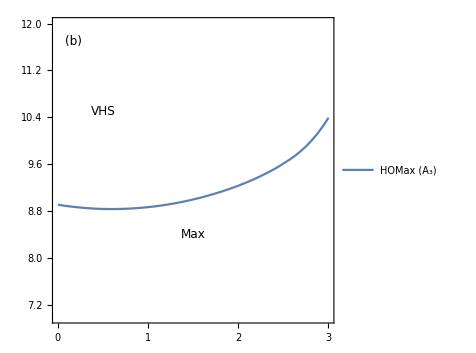

```mathematica
FitFunc4=Interpolation[HosListBand8p2];
PlotBand8p2=ListPlot[HosListBand8p2];
PanelB=Show[(*PlotBand9,*)Plot[FitFunc4[x],{x,0,3},FrameLabel->{(*"Δ_nem(%)"*)None,(*"θ(°)"*)None},PlotLegends->Placed[{Style["HOMax (A_3)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{0,3},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{0,1,2,3},None}}],Graphics[Text[Style["Max",FontFamily->"Arial",FontSize->12],{1.5,8.4}]],Graphics[Text[Style["VHS",FontFamily->"Arial",FontSize->12],{0.5,10.5}]],Graphics[Text[Style["(b)",FontFamily->"Arial",FontSize->12],{0.175,11.7}]]]
```

## Finding HOVHs at the M point

### Bands 7 & 8

```mathematica
HosListBand8M={};
SetSharedVariable[HosListBand8M];

ParallelDo[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],Delt];

θCurr=9.5;
CurrResln=10^-2;
HOSFound=False;
NoTry=1;

While[NoTry<=4&&HOSFound==False,
TaylorPoly=Chop[TaylorExpandBand[HamCurr(*The Hamiltonian*),{0,π//N,θCurr}(*the (k,t) point at which we are going to series expand.*),8(*Band to series expand*),2(*Degree of Taylor polynomial*),"Dimension"->2(*k-space dimension*),"TuningDegree"->2(*Degree of tuning parameter terms*),"TuningSymbol"->"δθ"(*Symbols for the tuning parameters*),"Resolution"->10^-4(*Resolution below which we shall kill terms*),"SampleDirection"->{0.333,0.779,0.1335}(*A sample k-vector that will be used for diagonalising symbolic matrices. This is not needed in principle since we will generate a random one in the routine if this is not provided*),"Messages"->False(*YesMessage*)],10^-6];

HesDet=(D[TaylorPoly[[1,3]],{p1,2}]D[TaylorPoly[[1,3]],{p2,2}]-(D[TaylorPoly[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[Chop[ReplaceAll[HesDet,{δθ->0}],CurrResln]==0,
HOSFound=True;
];

δθSolns=Solve[HesDet==0,δθ,Reals];

MinSoln=1;
Do[
If[Abs[ReplaceAll[δθ,δθSolns[[l]]]]<Abs[ReplaceAll[δθ,δθSolns[[MinSoln]]]],
MinSoln=l;
]
,{l,1,Length[δθSolns]}];

θCurr=θCurr+δθ/.δθSolns[[MinSoln]];
];

If[HOSFound==True,
TaylorPoly=Chop[TaylorExpandBand[HamCurr(*The Hamiltonian*),{0,π//N,θCurr}(*the (k,t) point at which we are going to series expand.*),8(*Band to series expand*),4(*Degree of Taylor polynomial*),"Dimension"->2(*k-space dimension*),"TuningDegree"->0(*Degree of tuning parameter terms*),"TuningSymbol"->"δθ"(*Symbols for the tuning parameters*),"Resolution"->10^-4(*Resolution below which we shall kill terms*),"SampleDirection"->{0.333,0.779,0.1335}(*A sample k-vector that will be used for diagonalising symbolic matrices. This is not needed in principle since we will generate a random one in the routine if this is not provided*),"Messages"->False(*YesMessage*)],10^-6];

Print["Δ_nem = ",Delt,"%. HOS found after ",NoTry," iterations. θ_crit = ",θCurr,".\n\t Tayl = ",Total[Chop[ReplaceAll[TaylorPoly[[1]],{p1->Subscript[k, x],p2->Subscript[k, y],δθ->0}],CurrResln]]];
AppendTo[HosListBand8M,{Delt,θCurr}];
,
Print[Style["No HOS found in the range!",Red]];
];

,{Delt,0,3,0.25}]
```

Δ_nem = 1.%. HOS found after 1 iterations. θ_crit = 9.85442.
	 Tayl = -16.0515+14.7302 k_x^2-6.16167 k_x^4+2.64509 k_x^2 k_y^2-98.8283 k_y^4

Δ_nem = 2.5%. HOS found after 1 iterations. θ_crit = 10.676.
	 Tayl = -1.1203+14.7639 k_x^2-0.225672 k_x^4-0.0179831 k_x^3 k_y-5.33457 k_x^2 k_y^2-91.083 k_y^4

Δ_nem = 2.%. HOS found after 1 iterations. θ_crit = 10.3027.
	 Tayl = -6.92537+14.5612 k_x^2-2.98365 k_x^4-0.010227 k_x^3 k_y-1.36728 k_x^2 k_y^2-95.0764 k_y^4

Δ_nem = 0.5%. HOS found after 1 iterations. θ_crit = 9.78813.
	 Tayl = -21.4024+14.8884 k_x^2-6.00748 k_x^4+1.98426 k_x^2 k_y^2-98.6179 k_y^4

Δ_nem = 2.75%. HOS found after 1 iterations. θ_crit = 10.8872.
	 Tayl = 4.11285+15.0951 k_x^2+1.19856 k_x^4-0.0104415 k_x^3 k_y-7.71679 k_x^2 k_y^2-88.1494 k_y^4

Δ_nem = 1.5%. HOS found after 1 iterations. θ_crit = 10.0271.
	 Tayl = -11.3397+14.6045 k_x^2-5.04298 k_x^4+1.31691 k_x^2 k_y^2-97.5853 k_y^4

Δ_nem = 3.%. HOS found after 1 iterations. θ_crit = 11.0942.
	 Tayl = 12.1443+15.6561 k_x^2+2.53934 k_x^4+0.0126962 k_x^3 k_y-10.2735 k_x^2 k_y^2-84.2225 k_y^4

Δ_nem = 1.25%. HOS found after 1 iterations. θ_crit = 9.92773.
	 Tayl = -13.6311+14.6612 k_x^2-5.7261 k_x^4+2.1578 k_x^2 k_y^2-98.3617 k_y^4

Δ_nem = 0.%. HOS found after 1 iterations. θ_crit = 9.84004.
	 Tayl = -27.6633-98.7668 k_x^4+15.2032 k_y^2+4.52407 k_x^2 k_y^2-8.08155 k_y^4

Δ_nem = 2.25%. HOS found after 1 iterations. θ_crit = 10.4782.
	 Tayl = -4.45347+14.6106 k_x^2-1.65792 k_x^4-0.0156096 k_x^3 k_y-3.2007 k_x^2 k_y^2-93.3075 k_y^4

Δ_nem = 0.75%. HOS found after 1 iterations. θ_crit = 9.80776.
	 Tayl = -18.6317+14.8069 k_x^2-6.30955 k_x^4+2.69655 k_x^2 k_y^2-98.9632 k_y^4

Δ_nem = 1.75%. HOS found after 1 iterations. θ_crit = 10.1522.
	 Tayl = -9.13606+14.5672 k_x^2-4.12422 k_x^4+0.140926 k_x^2 k_y^2-96.4934 k_y^4

Δ_nem = 0.25%. HOS found after 1 iterations. θ_crit = 9.79559.
	 Tayl = -24.3922+14.9735 k_x^2-4.34226 k_x^4-1.32057 k_x^2 k_y^2-96.8826 k_y^4

```mathematica
HosListBand8M=SortBy[HosListBand8M,First]
```

{{0.,9.84004},{0.25,9.79559},{0.5,9.78813},{0.75,9.80776},{1.,9.85442},{1.25,9.92773},{1.5,10.0271},{1.75,10.1522},{2.,10.3027},{2.25,10.4782},{2.5,10.676},{2.75,10.8872},{3.,11.0942}}

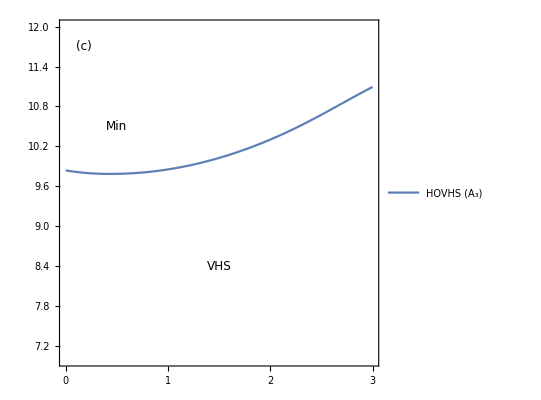

```mathematica
FitFunc5=Interpolation[HosListBand8M];
PlotBand8p3=ListPlot[HosListBand8M,AxesLabel->{"Δ_nem(%)","θ(°)"},PlotLegends->Placed[{"HOVHs (A_3)"},{0.5,0.965}]];
PanelC=Show[(*PlotBand9,*)Plot[FitFunc5[x],{x,0,3},FrameLabel->{(*"Δ_nem(%)","θ(°)"*)None,None},PlotLegends->Placed[{Style["HOVHS (A_3)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{0,3},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{0,1,2,3},None}}],Graphics[Text[Style["VHS",FontFamily->"Arial",FontSize->12],{1.5,8.4}]],Graphics[Text[Style["Min",FontFamily->"Arial",FontSize->12],{0.5,10.5}]],Graphics[Text[Style["(c)",FontFamily->"Arial",FontSize->12],{0.175,11.7}]]]
```

### Bands 9 & 10

```mathematica
HosListBand6M={};
SetSharedVariable[HosListBand6M];

ParallelDo[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],Delt];

θCurr=9.5;
CurrResln=10^-2;
HOSFound=False;
NoTry=1;

While[NoTry<=4&&HOSFound==False,
TaylorPoly=Chop[TaylorExpandBand[HamCurr(*The Hamiltonian*),{0,π//N,θCurr}(*the (k,t) point at which we are going to series expand.*),6(*Band to series expand*),2(*Degree of Taylor polynomial*),"Dimension"->2(*k-space dimension*),"TuningDegree"->2(*Degree of tuning parameter terms*),"TuningSymbol"->"δθ"(*Symbols for the tuning parameters*),"Resolution"->10^-4(*Resolution below which we shall kill terms*),"SampleDirection"->{0.333,0.779,0.1335}(*A sample k-vector that will be used for diagonalising symbolic matrices. This is not needed in principle since we will generate a random one in the routine if this is not provided*),"Messages"->False(*YesMessage*)],10^-6];

HesDet=(D[TaylorPoly[[1,3]],{p1,2}]D[TaylorPoly[[1,3]],{p2,2}]-(D[TaylorPoly[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[Chop[ReplaceAll[HesDet,{δθ->0}],CurrResln]==0,
HOSFound=True;
];

δθSolns=Solve[HesDet==0,δθ,Reals];

MinSoln=1;
Do[
If[Abs[ReplaceAll[δθ,δθSolns[[l]]]]<Abs[ReplaceAll[δθ,δθSolns[[MinSoln]]]],
MinSoln=l;
]
,{l,1,Length[δθSolns]}];

θCurr=θCurr+δθ/.δθSolns[[MinSoln]];
];

If[HOSFound==True,
TaylorPoly=Chop[TaylorExpandBand[HamCurr(*The Hamiltonian*),{0,π//N,θCurr}(*the (k,t) point at which we are going to series expand.*),6(*Band to series expand*),4(*Degree of Taylor polynomial*),"Dimension"->2(*k-space dimension*),"TuningDegree"->0(*Degree of tuning parameter terms*),"TuningSymbol"->"δθ"(*Symbols for the tuning parameters*),"Resolution"->10^-4(*Resolution below which we shall kill terms*),"SampleDirection"->{0.333,0.779,0.1335}(*A sample k-vector that will be used for diagonalising symbolic matrices. This is not needed in principle since we will generate a random one in the routine if this is not provided*),"Messages"->False(*YesMessage*)],10^-6];

Print["Δ_nem = ",Delt,"%. HOS found after ",NoTry," iterations. θ_crit = ",θCurr,".\n\t Tayl = ",Total[Chop[ReplaceAll[TaylorPoly[[1]],{p1->Subscript[k, x],p2->Subscript[k, y],δθ->0}],CurrResln]]];
AppendTo[HosListBand6M,{Delt,θCurr}];
,
Print[Style["No HOS found in the range!",Red]];
];

,{Delt,0,3,0.25}]
```

Δ_nem = 1.%. HOS found after 1 iterations. θ_crit = 9.80565.
	 Tayl = -18.3115-100.389 k_x^4+15.3957 k_y^2+6.3958 k_x^2 k_y^2-8.19816 k_y^4

Δ_nem = 2.5%. HOS found after 1 iterations. θ_crit = 10.5276.
	 Tayl = -7.08976-96.3126 k_x^4+0.0304409 k_x^3 k_y+16.292 k_y^2+7.01689 k_x^2 k_y^2-0.015326 k_x k_y^3-6.81202 k_y^4

Δ_nem = 2.%. HOS found after 1 iterations. θ_crit = 10.1907.
	 Tayl = -11.2329-98.1961 k_x^4+0.0167324 k_x^3 k_y+15.8689 k_y^2+6.43314 k_x^2 k_y^2-0.0122696 k_x k_y^3-7.26008 k_y^4

Δ_nem = 2.75%. HOS found after 1 iterations. θ_crit = 10.7272.
	 Tayl = -3.57871-95.0433 k_x^4+0.0288984 k_x^3 k_y+16.6474 k_y^2+7.59568 k_x^2 k_y^2-0.0122503 k_x k_y^3-6.80334 k_y^4

Δ_nem = 0.5%. HOS found after 1 iterations. θ_crit = 9.76426.
	 Tayl = -22.5278-101.247 k_x^4+15.2214 k_y^2+7.54739 k_x^2 k_y^2-8.86719 k_y^4

Δ_nem = 1.5%. HOS found after 1 iterations. θ_crit = 9.94961.
	 Tayl = -14.6564-99.5305 k_x^4+15.5997 k_y^2+6.24236 k_x^2 k_y^2-7.76804 k_y^4

Δ_nem = 3.%. HOS found after 1 iterations. θ_crit = 10.9341.
	 Tayl = 2.19695-93.3049 k_x^4+0.0105083 k_x^3 k_y+17.1833 k_y^2+8.54108 k_x^2 k_y^2-7.12536 k_y^4

Δ_nem = 1.25%. HOS found after 1 iterations. θ_crit = 9.86521.
	 Tayl = -16.4337-100.007 k_x^4+15.4922 k_y^2+6.26773 k_x^2 k_y^2-7.98998 k_y^4

Δ_nem = 0.%. HOS found after 1 iterations. θ_crit = 9.84004.
	 Tayl = -27.6633-98.7668 k_x^4+15.2032 k_y^2+4.52407 k_x^2 k_y^2-8.08155 k_y^4

Δ_nem = 2.25%. HOS found after 1 iterations. θ_crit = 10.3474.
	 Tayl = -9.39628-97.3302 k_x^4+0.0242414 k_x^3 k_y+16.0497 k_y^2+6.66007 k_x^2 k_y^2-0.0146498 k_x k_y^3-7.00332 k_y^4

Δ_nem = 0.75%. HOS found after 1 iterations. θ_crit = 9.77175.
	 Tayl = -20.3288-100.741 k_x^4+15.3063 k_y^2+6.71231 k_x^2 k_y^2-8.43553 k_y^4

Δ_nem = 1.75%. HOS found after 1 iterations. θ_crit = 10.0582.
	 Tayl = -12.9416-98.9297 k_x^4+0.0105295 k_x^3 k_y+15.723 k_y^2+6.29789 k_x^2 k_y^2-7.52287 k_y^4

Δ_nem = 0.25%. HOS found after 1 iterations. θ_crit = 9.78358.
	 Tayl = -24.9486-102.832 k_x^4+15.14 k_y^2+10.7305 k_x^2 k_y^2-10.4072 k_y^4

```mathematica
HosListBand6M=SortBy[HosListBand6M,First]
```

{{0.,9.84004},{0.25,9.78358},{0.5,9.76426},{0.75,9.77175},{1.,9.80565},{1.25,9.86521},{1.5,9.94961},{1.75,10.0582},{2.,10.1907},{2.25,10.3474},{2.5,10.5276},{2.75,10.7272},{3.,10.9341}}

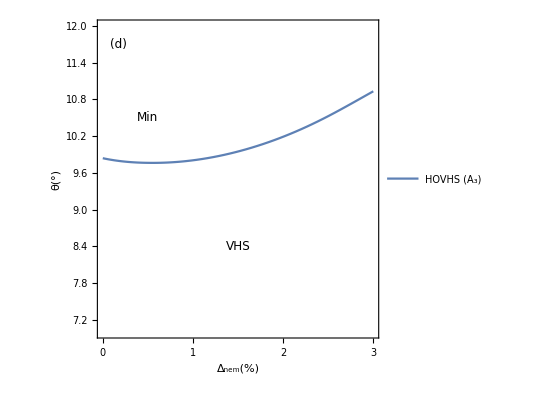

```mathematica
FitFunc6=Interpolation[HosListBand6M];
PlotBand6=ListPlot[HosListBand6M,AxesLabel->{"Δ_nem(%)","θ(°)"},PlotLegends->Placed[{"HOVHs (A_3)"},{0.5,0.965}]];
PanelD=Show[(*PlotBand9,*)Plot[FitFunc6[x],{x,0,3},FrameLabel->{"Δ_nem(%)","θ(°)"},PlotLegends->Placed[{Style["HOVHS (A_3)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{0,3},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{0,1,2,3},None}}],Graphics[Text[Style["VHS",FontFamily->"Arial",FontSize->12],{1.5,8.4}]],Graphics[Text[Style["Min",FontFamily->"Arial",FontSize->12],{0.5,10.5}]],Graphics[Text[Style["(d)",FontFamily->"Arial",FontSize->12],{0.175,11.7}]]]
```

## Assembling the results

### Labeling the critical points of interest

```mathematica
Bnd4=GenerateBandStructure[HamTempNem2,HSymmPts,"OrbitalProjection"->True,"OrbitalGrouping"->{{1,4,7,10},{2,5,8,11},{3,6,9,12}}];
```

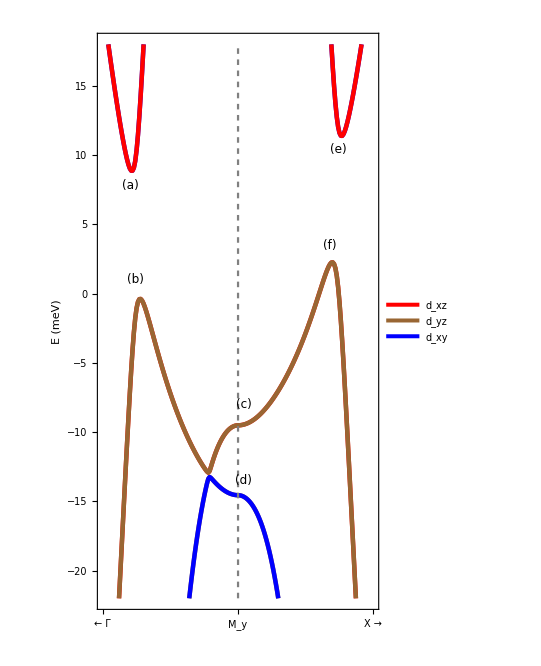

```mathematica
PltCritPts=PlotBandStructure[Bnd3,(*{-0.042,0.012}*){-22,18},AspectRatio->5/3,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)13,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{13,Black,"Arial"},"yTicks"->{12,Black,"Helvetica"},"LineThickness"->0.008,"LineColorScheme"->{Red,Brown,Blue},(*Dividing Lines*)"DividingLines"->{(*Dashing[..]*)0.01,(*Color*)Gray,(*Thickness*)0.004},(*,Legend*)"PlotKeyLegend"->{{"d_xz","d_yz","d_xy"},{0.25,0.8}}];
PanelCritPts=Show[PltCritPts,Graphics[Text[Style["(a)",FontFamily->"Arial",FontSize->12],{0.28,7.8}]],Graphics[Text[Style["(b)",FontFamily->"Arial",FontSize->12],{0.34,1}]],Graphics[Text[Style["(c)",FontFamily->"Arial",FontSize->12],{1.45,-8}]],Graphics[Text[Style["(d)",FontFamily->"Arial",FontSize->12],{1.45,-13.5}]],Graphics[Text[Style["(e)",FontFamily->"Arial",FontSize->12],{2.43,10.42}]],Graphics[Text[Style["(f)",FontFamily->"Arial",FontSize->12],{2.34,3.5}]]]
```

### Phase diagrams for the critical points

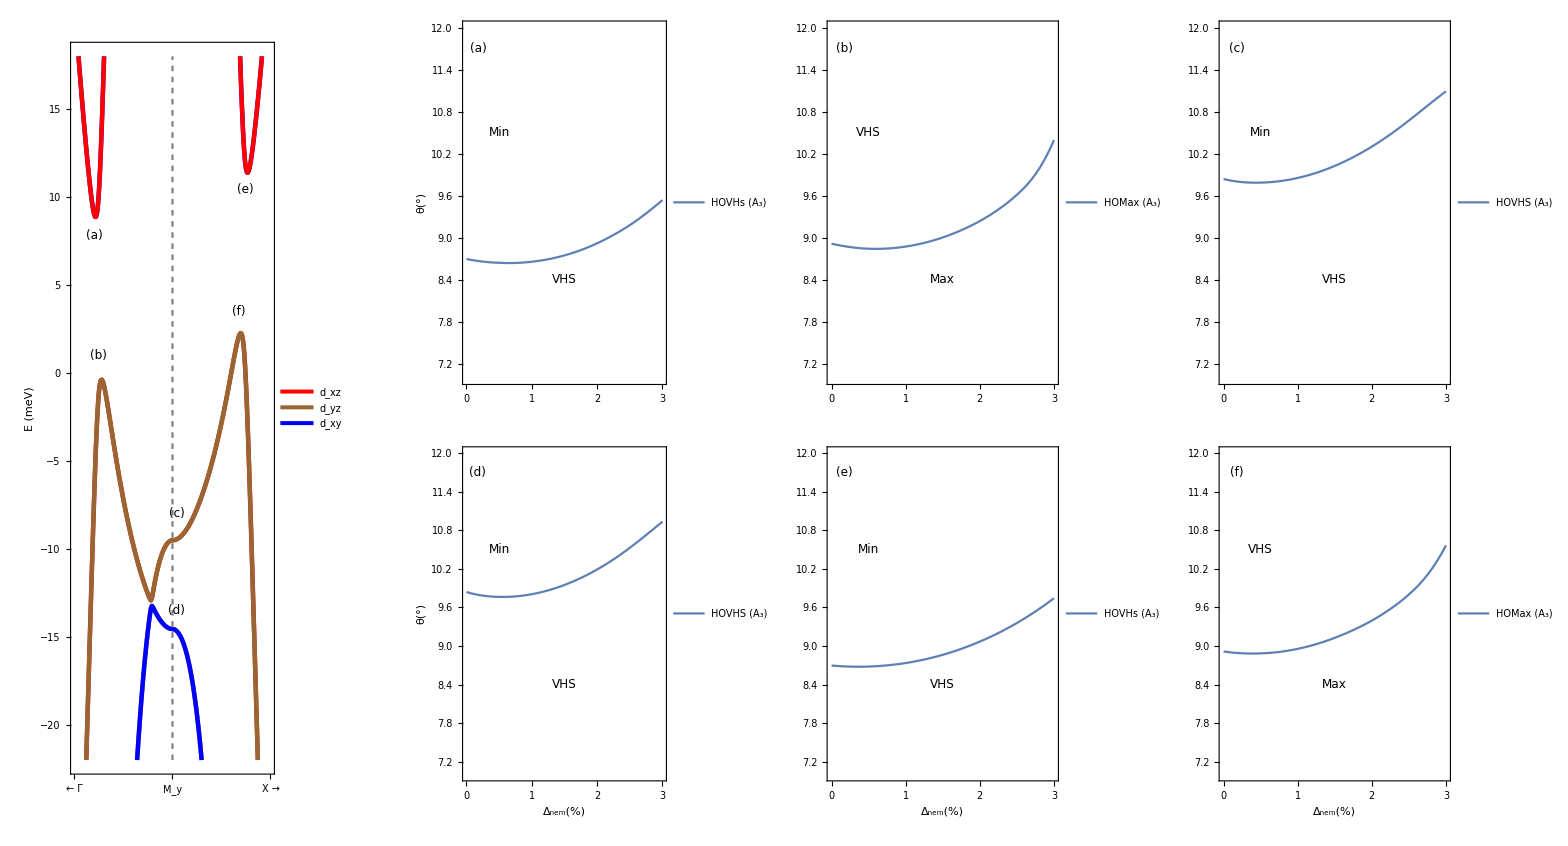

```mathematica
Show[GraphicsGrid[{{PanelCritPts,PanelA,PanelB,PanelC},{SpanFromAbove,PanelD,PanelE,PanelF}},Spacings->{Scaled[0.],Scaled[0.02]}],ImageSize->Full]
```

We can also examine the orbital-projected band structure in the absence of nematicity and compare with the nematic model

```mathematica
BndTemp=GenerateBandStructure[HamTemp,HSymmPts,"OrbitalProjection"->True,"OrbitalGrouping"->{{1,4,7,10},{2,5,8,11},{3,6,9,12}}];
```

```mathematica
PltTemp=PlotBandStructure[BndTemp,(*{-0.042,0.012}*){-28,18},AspectRatio->5/3,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)13,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{13,Black,"Arial"},"yTicks"->{12,Black,"Helvetica"},"LineThickness"->0.008,"LineColorScheme"->{Red,Brown,Blue},(*Dividing Lines*)"DividingLines"->{(*Dashing[..]*)0.01,(*Color*)Gray,(*Thickness*)0.004},(*,Legend*)"PlotKeyLegend"->{{"d_xz","d_yz","d_xy"},{0.25,0.8}}];
```

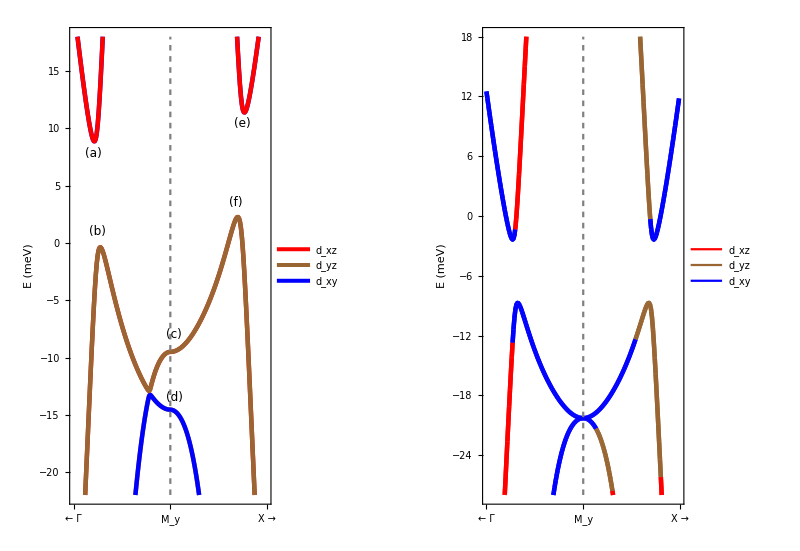

```mathematica
GraphicsRow[{PanelCritPts,PltTemp}]
```

The dominant orbitals seem to have changed. (Note that we have computed the total contribution of each type of orbital across both the Ru atoms and both spin species).

## Phase diagrams

We will now generate the phase diagram for the SOC gap singularities that is included in the manuscript

```mathematica
θmin=7;
θmax=12(*9.6*);

cm=72/2.54;

TicsFontSize=6;
AxesFontSize=8;
RegionFontColour=LightGray;
FigLength=3.5cm;
LeftPadding=0.5cm;
RightPadding=0.2cm;
BottomPadding=0.5cm;
TopPadding=0.15cm;
xTicsLabeled={{7,"7"},{8,"8"},{9,"9"},{10,"10"},{11,"11"},{12,"12"}};
xTics={7,8,9,10,11,12};

VHsColour={((*125*)161)/255,((*9*)93)/255,((*184*)216)/255,1(*0.65*)};
MinColour={((*9*)59)/255,((*73*)96)/255,((*184*)196)/255,1(*0.65*)};
MaxColour={((*207*)242)/255,((*17*)70)/255,((*51*)70)/255,1(*0.65*)};

PanA=ParametricPlot[{{v FitFunc3[u]+θmin(1-v),u},{(1-v)FitFunc3[u]+θmax v,u}},{u,0,4},{v,0,1},PlotRange->{{θmin,θmax},{0,4}},Frame->True,PlotStyle->{RGBColor[VHsColour],RGBColor[MinColour]},AspectRatio->1,(*FrameTicks->{True,True},*)(*FrameLabel->{None,Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black]},*)FrameTicksStyle->{Directive[Black,FontFamily->"Arial",TicsFontSize],{Directive[FontOpacity->0,FontSize->0],Directive[FontOpacity->0,FontSize->0]}},FrameTicks->{True,{xTics,xTics}},ImagePadding->{{LeftPadding,RightPadding},{0.6TopPadding,TopPadding}},ImageSize->FigLength];

PanAp2=ParametricPlot[{FitFunc3[u],u},{u,0,4},Axes->False,Frame->False,PlotStyle->{Black,Thickness[0.018]},PlotRange->{{θmin,θmax},{0,4}},PlotLegends->Placed[LineLegend[{Style["A_3",FontFamily->"Arial",FontSize->TicsFontSize,FontColor->RegionFontColour]},LegendMarkerSize->{10,1.3}],{{0.25,0.92},{0.5,0.5}}]];

Labeled[Show[PanA,PanAp2],{Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black],""},{Left,Bottom},Spacings->{0, 0},RotateLabel->True]


PanB=ParametricPlot[{{v FitFunc4[u]+θmin(1-v),u},{(1-v)FitFunc4[u]+θmax v,u}},{u,0,4},{v,0,1},PlotRange->{{θmin,θmax},{0,4}},Frame->True,PlotStyle->{RGBColor[MaxColour],RGBColor[VHsColour]},AspectRatio->1,FrameTicksStyle->{Directive[Black,FontFamily->"Arial",TicsFontSize],{Directive[Black,FontFamily->"Arial",TicsFontSize],Directive[FontOpacity->0,FontSize->0]}},FrameTicks->{True,{xTicsLabeled,xTics}},ImagePadding->{{LeftPadding,RightPadding},{BottomPadding,0.5TopPadding}},ImageSize->FigLength];

PanBp2=ParametricPlot[{FitFunc4[u],u},{u,0,4},Axes->False,Frame->False,PlotStyle->{Black,Thickness[0.018]},PlotLegends->Placed[LineLegend[{Style["A_3",FontFamily->"Arial",FontSize->TicsFontSize,FontColor->RegionFontColour]},LegendMarkerSize->{10,1.3}],{{0.25,0.92},{0.5,0.5}}]];

Labeled[Show[PanB,PanBp2],{Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black],Style["θ (°)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black]},{Left,Bottom},Spacings->{0, 0},RotateLabel->True]
```

-Graphics-Δ_nem (%)

-Graphics-Δ_nem (%)θ (°)

```mathematica
PhaseDiagramFinal=GraphicsGrid[{{Labeled[Show[PanA,PanAp2,Graphics[Rotate[Text[Style["Saddle",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{8,2}],90Degree]],Graphics[Text[Style["Minimum",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{10.5,2.0}]],ListPlot[{{9,0.5}},PlotMarkers->{▲,2.5},PlotStyle->{LightGray,Thickness[0.02]}],Graphics[Text[Style["QPI",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->(TicsFontSize-1)],{9.5,0.45}]],ListPlot[{{8,0.16}},PlotMarkers->{"↓",8},PlotStyle->{LightGray}],Graphics[Text[Style["ARPES",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->(TicsFontSize-1)],{7.9,0.5}]]],{Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black]},{Left},Spacings->{0.1, 0},RotateLabel->True]
},{Labeled[Show[PanB,PanBp2,Graphics[Rotate[Text[Style["Maximum",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{8,2}],90Degree]],Graphics[Text[Style["Saddle",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{10.5,2.0}]],ListPlot[{{9,0.5}},PlotMarkers->{▲,2.5},PlotStyle->{LightGray,Thickness[0.02]}],Graphics[Text[Style["QPI",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->(TicsFontSize-1)],{9.5,0.45}]],ListPlot[{{8,0.16}},PlotMarkers->{"↓",8},PlotStyle->{LightGray}],Graphics[Text[Style["ARPES",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->(TicsFontSize-1)],{7.9,0.5}]]],{Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black],Style["θ (°)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black]},{Left,Bottom},Spacings->{0.1, 0},RotateLabel->True]}},Spacings->{0,-8}]

Export[NotebookDirectory[]<>"Phase_horiz.pdf",Show[PhaseDiagramFinal,ImageSize->4.5cm]]
```

-Graphics-

/Users/phac/Research/GitHub/BandUtilities/Sr2RuO4/Phase_horiz.pdf